```mathematica
ClearAll;
Np=50;
coup="0.20";
Nrun=9;
filename=NotebookDirectory[]<>"data/circle/NP"<>ToString[Np]<> "/outxv_1_g"<>ToString[coup]<>"_n"<>ToString[Nrun]<>".dat";
T=Import[filename,"Table"];

steps=Length[T]/Np-1;
(* steps is number of pictures *)
```

```mathematica
spicture=3.;
```

```mathematica
(* let me plot x,y points, initial and final  *)
```

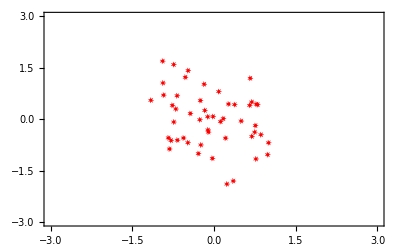
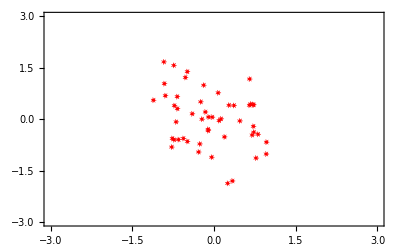
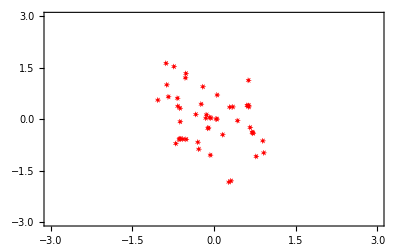
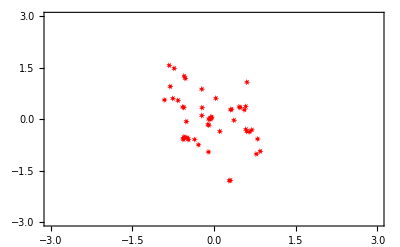
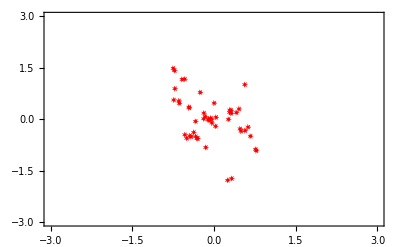
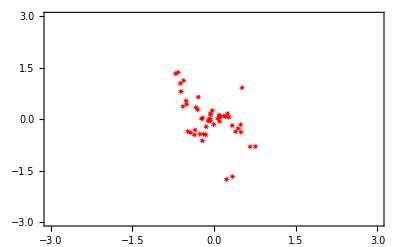
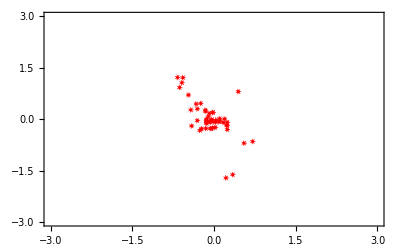
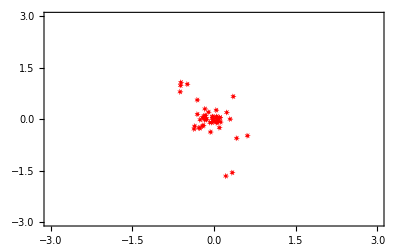

```mathematica
TablePlot=Table[ListPlot[{Table[{T[[i]][[1]],T[[i]][[2]]},{i,kadr*Np+1,kadr*Np+Np}]},PlotRange->{{-spicture, spicture},{-spicture,spicture}},Frame->True,PlotMarkers->Graphics[{EdgeForm[{Red,Thickness[.01],JoinForm[{"Miter",5}]}],Polygon[0.003 Table[{Cos[a],Sin[a]},{a,0,6 π,2 π 3/7}]]},PlotRangePadding->.5],PlotStyle->{Red}],{kadr,0,steps-1}]
```

```mathematica
vtot=Sum[T[[i]][[3]],{i,1,Np*80}]
```

0.00024

```mathematica
(* ok, total momentum is very close to zero ! *)
```

```mathematica
filename2=NotebookDirectory[]<>"data/circle/NP"<>ToString[Np]<> "/outenergy_1_g"<>ToString[coup]<>"_n"<>ToString[Nrun]<>".dat";
En=Import[filename2,"Table"];
```

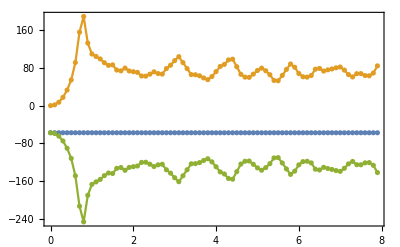

```mathematica
Show[{ListPlot[{  Table[{En[[i]][[1]],En[[i]][[2]]},{i,1,steps}], Table[{En[[i]][[1]],En[[i]][[3]]},{i,1,steps}],Table[{En[[i]][[1]],En[[i]][[4]]},{i,1,steps}]},Joined->True,Frame->True,LabelStyle->Directive[FontSize->20]],ListPlot[{  Table[{En[[i]][[1]],En[[i]][[2]]},{i,1,steps}], Table[{En[[i]][[1]],En[[i]][[3]]},{i,1,steps}],Table[{En[[i]][[1]],En[[i]][[4]]},{i,1,steps}]}]}]
```

```mathematica
(* I am interested in how distribution in kinetic energy looks like *)
```

```mathematica
A=Table[T[[i]][[3]]^2+T[[i]][[4]]^2,{i,1,Np*steps}];
vv=A[[1]] 
Nn=1
For[i=1,i<Np*steps,i++,If[A[[i]]>vv,vv=A[[i]]; Nn=i]]
vv
Nn
```

0.0644823

1

22.2345

378

```mathematica
(* now we want to find the corresponding picture number and read it *)
pictnumber=IntegerPart[Nn/Np]
```

7

```mathematica
A[[Nn]]
xc=T[[Nn]][[1]]
yc=T[[Nn]][[2]]
```

22.2345

-0.15211

0.0498

```mathematica
(* we found particle with maximal kinetic energy and its coordinates 
now I want to count how many particles are incide given radius r0 *)
```

```mathematica
r0=0.3;
Ninside=0;
For[i=1+pictnumber*Np,i<Np+pictnumber*Np,i++,If[(T[[i]][[1]]-xc)^2+(T[[i]][[2]]-yc)^2<r0^2, Ninside=Ninside+1]]
Ninside
density=Ninside/Pi/r0^2
```

30

106.103

```mathematica
(* I compared density inside given circle near maximal v^2 and at the beginning: it changed by factor 4 *)
```